```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# Other intertwiners

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.0.csv";
```

```mathematica
getfile[Dl_,K_]:=  StringJoin["../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_",ToString[Dl],"/frogface_pcutoff_",ToString[NumberForm[N[K],{3,1}]],".csv"];
```

```mathematica
getfile[0,1/2]
```

../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/propagator_matrix/bspin_0.5/cutoff_10.0/Dl_0/frogface_pcutoff_0.5.csv

```mathematica
NumberForm[N[2],{3,1}]
```

2.0

```mathematica
A00KDl0 = {};
A01KDl0 = {};
A11KDl0 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[0,k],"Data",HeaderLines->1];
AppendTo[A00KDl0,{k,tmp00}];
AppendTo[A01KDl0,{k,tmp01}];
AppendTo[A11KDl0,{k,tmp11}];
]
```

```mathematica
A00KDl1 = {};
A01KDl1 = {};
A11KDl1 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[1,k],"Data",HeaderLines->1];
AppendTo[A00KDl1,{k,tmp00}];
AppendTo[A01KDl1,{k,tmp01}];
AppendTo[A11KDl1,{k,tmp11}];
]
```

```mathematica
A00KDl2 = {};
A01KDl2 = {};
A11KDl2 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[2,k],"Data",HeaderLines->1];
AppendTo[A00KDl2,{k,tmp00}];
AppendTo[A01KDl2,{k,tmp01}];
AppendTo[A11KDl2,{k,tmp11}];
]
```

```mathematica
A00KDl3 = {};
A01KDl3 = {};
A11KDl3 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[3,k],"Data",HeaderLines->1];
AppendTo[A00KDl3,{k,tmp00}];
AppendTo[A01KDl3,{k,tmp01}];
AppendTo[A11KDl3,{k,tmp11}];
]
```

```mathematica
A00KDl4 = {};
A01KDl4 = {};
A11KDl4 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[4,k],"Data",HeaderLines->1];
AppendTo[A00KDl4,{k,tmp00}];
AppendTo[A01KDl4,{k,tmp01}];
AppendTo[A11KDl4,{k,tmp11}];
]
```

```mathematica
A00KDl5 = {};
A01KDl5 = {};
A11KDl5 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[5,k],"Data",HeaderLines->1];
AppendTo[A00KDl5,{k,tmp00}];
AppendTo[A01KDl5,{k,tmp01}];
AppendTo[A11KDl5,{k,tmp11}];
]
```

```mathematica
A00KDl6 = {};
A01KDl6 = {};
A11KDl6 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[6,k],"Data",HeaderLines->1];
AppendTo[A00KDl6,{k,tmp00}];
AppendTo[A01KDl6,{k,tmp01}];
AppendTo[A11KDl6,{k,tmp11}];
]
```

```mathematica
A00KDl7 = {};
A01KDl7 = {};
A11KDl7 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[7,k],"Data",HeaderLines->1];
AppendTo[A00KDl7,{k,tmp00}];
AppendTo[A01KDl7,{k,tmp01}];
AppendTo[A11KDl7,{k,tmp11}];
]
```

```mathematica
A00KDl8 = {};
A01KDl8 = {};
A11KDl8 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[8,k],"Data",HeaderLines->1];
AppendTo[A00KDl8,{k,tmp00}];
AppendTo[A01KDl8,{k,tmp01}];
AppendTo[A11KDl8,{k,tmp11}];
]
```

```mathematica
A00KDl9 = {};
A01KDl9 = {};
A11KDl9 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[9,k],"Data",HeaderLines->1];
AppendTo[A00KDl9,{k,tmp00}];
AppendTo[A01KDl9,{k,tmp01}];
AppendTo[A11KDl9,{k,tmp11}];
]
```

```mathematica
A00KDl10 = {};
A01KDl10 = {};
A11KDl10 = {};
For[k=0, k ≤10, k+=1/2,
{{tmp00,tmp01},{tmp10,tmp11}}=Transpose@Import[getfile[10,k],"Data",HeaderLines->1];
AppendTo[A00KDl10,{k,tmp00}];
AppendTo[A01KDl10,{k,tmp01}];
AppendTo[A11KDl10,{k,tmp11}];
]
```

```mathematica
Clear[k]
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

{0.,3.68532×10^-8,1.85466×10^-7,2.17674×10^-7,2.32455×10^-7,2.40614×10^-7,2.45588×10^-7,2.4885×10^-7,2.51107×10^-7,2.52732×10^-7,2.5394×10^-7,2.5486×10^-7,2.55577×10^-7,2.56144×10^-7,2.56601×10^-7,2.56973×10^-7,2.57279×10^-7,2.57534×10^-7,2.57748×10^-7,2.57929×10^-7,2.58084×10^-7}

```mathematica
rExtrapolation00= Aitken/@Transpose[{Last/@A00KDl0,Last/@A00KDl1,Last/@A00KDl2,Last/@A00KDl3,Last/@A00KDl4,Last/@A00KDl5,Last/@A00KDl6,Last/@A00KDl7,Last/@A00KDl8,Last/@A00KDl9,Last/@A00KDl10}]
rExtrapolation01=Aitken/@Transpose[{Last/@A01KDl0,Last/@A01KDl1,Last/@A01KDl2,Last/@A01KDl3,Last/@A01KDl4,Last/@A01KDl5,Last/@A01KDl6,Last/@A01KDl7,Last/@A01KDl8,Last/@A01KDl9,Last/@A01KDl10}]
rExtrapolation11=Aitken/@Transpose[{Last/@A11KDl0,Last/@A11KDl1,Last/@A11KDl2,Last/@A11KDl3,Last/@A11KDl4,Last/@A11KDl5,Last/@A11KDl6,Last/@A11KDl7,Last/@A11KDl8,Last/@A11KDl9,Last/@A11KDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,3.79314×10^-8,1.91872×10^-7,2.26226×10^-7,2.42425×10^-7,2.5169×10^-7,2.57555×10^-7,2.6155×10^-7,2.64417×10^-7,2.66556×10^-7,2.68199×10^-7,2.69492×10^-7,2.70529×10^-7,2.71374×10^-7,2.72071×10^-7,2.72653×10^-7,2.73144×10^-7,2.73561×10^-7,2.73918×10^-7,2.74227×10^-7,2.74495×10^-7}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,-1.18525×10^-22,-1.46297×10^-22,-4.00803×10^-22,-6.78105×10^-22,-7.85208×10^-22,-9.94979×10^-22,-1.24761×10^-21,-1.65565×10^-21,-1.2905×10^-21,-1.31866×10^-21,-1.536×10^-21,-1.4579×10^-21,-1.59453×10^-21,-1.5962×10^-21,-1.69321×10^-21,-1.61988×10^-21,-1.60971×10^-21,-1.60124×10^-21,-1.58227×10^-21,-1.52566×10^-21}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,5.90753×10^-8,4.19544×10^-8,5.04902×10^-8,5.19978×10^-8,5.31053×10^-8,5.39754×10^-8,5.46688×10^-8,5.52273×10^-8,5.56825×10^-8,5.60575×10^-8,5.63696×10^-8,5.66319×10^-8,5.6854×10^-8,5.70437×10^-8,5.72068×10^-8,5.73478×10^-8,5.74705×10^-8,5.75778×10^-8,5.76721×10^-8,5.77553×10^-8}

```mathematica
Extrapolation00=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation00];
Extrapolation01=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation01];
Extrapolation11=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation11];
```

### Intertwiners 00

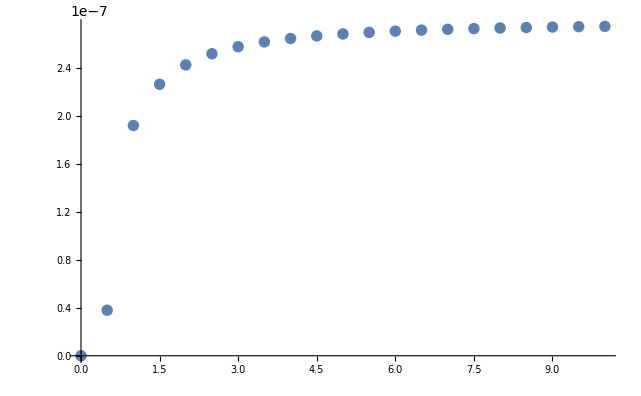

```mathematica
ListPlot[{Extrapolation00}]
```

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[2.92746×10^-7-(1.7681×10^-8)/k^2-(8.61094×10^-8)/k-4.1148×10^-9 Log[k]]

```mathematica
fitExtrap00=NonlinearModelFit[Extrapolation00[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[2.80275×10^-7-(5.02632×10^-8)/k^2-(5.0882×10^-8)/k]

```mathematica
fitExtrap00["ParameterConfidenceIntervals"]
```

{{2.79928×10^-7,2.80622×10^-7},{-5.38666×10^-8,-4.78975×10^-8},{-5.55173×10^-8,-4.50092×10^-8}}

```mathematica
fit1 =First/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap00["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

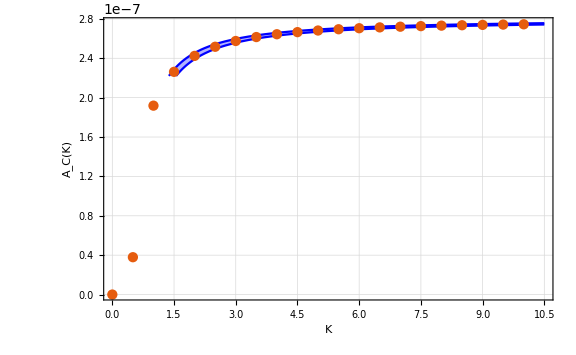

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation00,PlotRange->All],PlotRange->All]
```

### Intertwiners 11

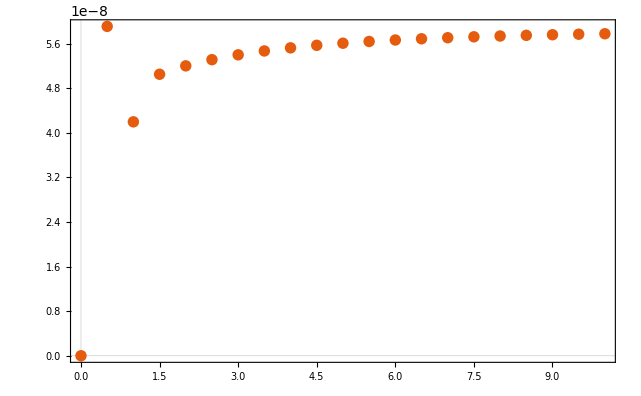

```mathematica
ListPlot[{Extrapolation11}]
```

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[6.21657×10^-8+(1.64103×10^-8)/k^2-(2.74317×10^-8)/k-7.92771×10^-10 Log[k]]

```mathematica
fitExtrap11=NonlinearModelFit[Extrapolation11[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[5.97628×10^-8+(1.01329×10^-8)/k^2-(2.06447×10^-8)/k]

```mathematica
fitExtrap11["ParameterConfidenceIntervals"]
```

{{5.96944×10^-8,5.98312×10^-8},{-2.1233×10^-8,-2.00564×10^-8},{9.09726×10^-9,1.11685×10^-8}}

```mathematica
fit1 =First/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap11["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

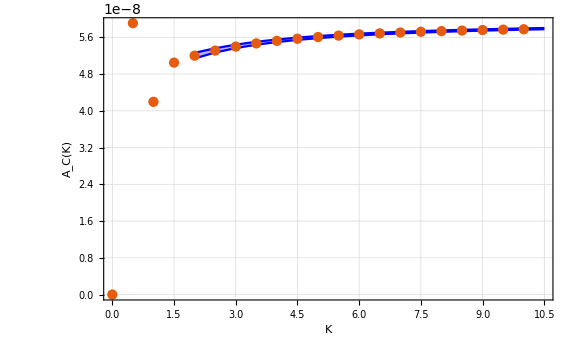

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation11,PlotRange->All],PlotRange->All]
```

### Intertwiners 01

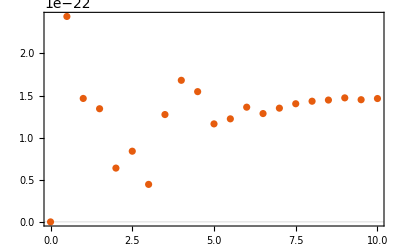

```mathematica
ListPlot[{A01KDl10}]
```

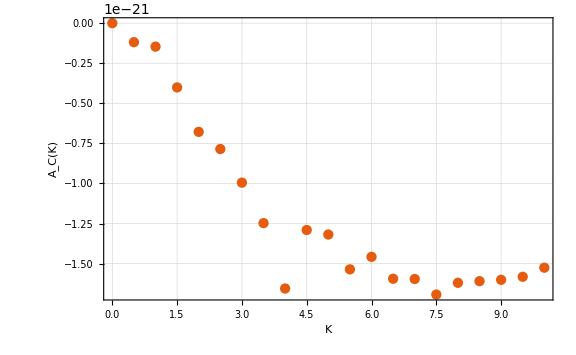

```mathematica
ListPlot[Extrapolation01,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

# Immirzi 0.1 and dimension (2j+1)^2

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_0.1/divergence/cutoff_10.0/frogface_Dl_min_0_Dl_max_10_dim_2.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,2.53856×10^-7,9.0241×10^-7,1.4765×10^-6,2.75382×10^-6,4.36398×10^-6,6.29697×10^-6,8.54756×10^-6,0.0000111127,0.0000139904,0.0000171795,0.0000206789,0.0000244881,0.0000286065,0.0000330337,0.0000377694,0.0000428134,0.0000481654,0.0000538253,0.0000597929,0.0000660682}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,2.53856×10^-7},{1,9.0241×10^-7},{3/2,1.4765×10^-6},{2,2.75382×10^-6},{5/2,4.36398×10^-6},{3,6.29697×10^-6},{7/2,8.54756×10^-6},{4,0.0000111127},{9/2,0.0000139904},{5,0.0000171795},{11/2,0.0000206789},{6,0.0000244881},{13/2,0.0000286065},{7,0.0000330337},{15/2,0.0000377694},{8,0.0000428134},{17/2,0.0000481654},{9,0.0000538253},{19/2,0.0000597929},{10,0.0000660682}}

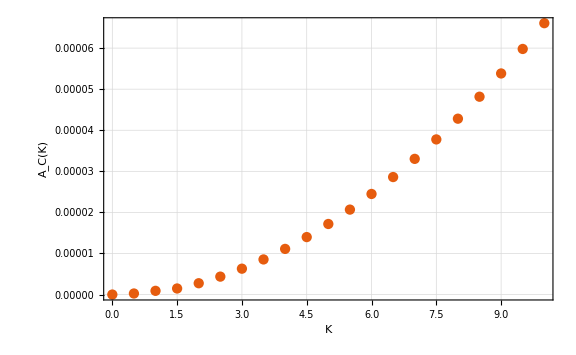

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],a k^3+ b k^2 + c k+ d,{a,b,c,d},k]
```

FittedModel[-5.73835×10^-7+3.91509×10^-7 k+6.36217×10^-7 k^2-8.98924×10^-10 k^3]

```mathematica
(Normal[fitExtrap]/.Plus->List)/.k->10
```

{-5.73835×10^-7,3.91509×10^-6,0.0000636217,-8.98924×10^-7}

```mathematica
fitExtrap["BestFitParameters"]
```

{a→-8.98924×10^-10,b→6.36217×10^-7,c→3.91509×10^-7,d→-5.73835×10^-7}

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],c (1+ a  k + b k^2+ e Log[k]),{a,b,c,e},k]
```

FittedModel[-7.02195×10^-7 (1-0.905194 k-0.873047 k^2+0.551006 Log[k])]

```mathematica
fitExtrap["RSquared"]
```

1.

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],c (1+ a  k + b k^2),{a,b,c},k]
```

FittedModel[-7.50852×10^-7 (1-0.65493 k-0.824549 k^2)]

```mathematica
fitExtrap["RSquared"]
```

1.

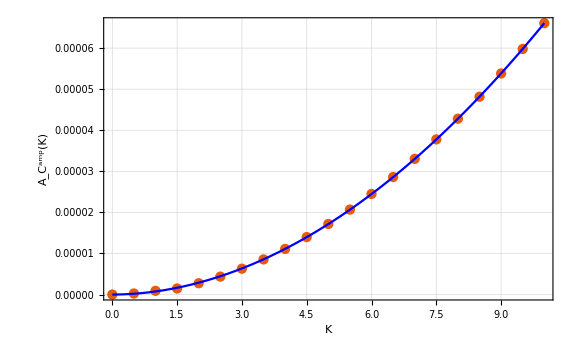

```mathematica
Show[ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C^amp(K)"},ImageSize->Large],Plot[Normal@fitExtrap,{k,0,10},PlotStyle->Blue]]
```

# Immirzi 1

## Load the Data

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../CLUSTER_COMPUTATIONS/data/EPRL/immirzi_1.0/divergence/cutoff_10.0/frogface_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,5.22887×10^-14,3.18227×10^-13,4.4819×10^-13,5.3846×10^-13,6.07705×10^-13,6.62165×10^-13,7.06014×10^-13,7.42028×10^-13,7.72103×10^-13,7.97573×10^-13,8.19399×10^-13,8.38292×10^-13,8.5479×10^-13,8.69302×10^-13,8.82152×10^-13,8.93595×10^-13,9.03834×10^-13,9.13038×10^-13,9.21343×10^-13,9.28863×10^-13}

```mathematica
Extrapolationg1=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1,10,1/2}]&@rExtrapolation]
```

{{0,0},{1,3.18227×10^-13},{3/2,4.4819×10^-13},{2,5.3846×10^-13},{5/2,6.07705×10^-13},{3,6.62165×10^-13},{7/2,7.06014×10^-13},{4,7.42028×10^-13},{9/2,7.72103×10^-13},{5,7.97573×10^-13},{11/2,8.19399×10^-13},{6,8.38292×10^-13},{13/2,8.5479×10^-13},{7,8.69302×10^-13},{15/2,8.82152×10^-13},{8,8.93595×10^-13},{17/2,9.03834×10^-13},{9,9.13038×10^-13},{19/2,9.21343×10^-13},{10,9.28863×10^-13}}

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.00446×10^-12+(9.26324×10^-13)/k^2-(1.419×10^-12)/k+2.49158×10^-14 Log[k]]

```mathematica
fitExtrapg1=NonlinearModelFit[Extrapolationg1[[5;;]], b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.08251×10^-12+(1.18749×10^-12)/k^2-(1.65993×10^-12)/k]

```mathematica
fitExtrapg1["ParameterConfidenceIntervals"]
```

{{1.08046×10^-12,1.08456×10^-12},{-1.67981×10^-12,-1.64005×10^-12},{1.14594×10^-12,1.22905×10^-12}}

```mathematica
fit1 =First/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrapg1["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

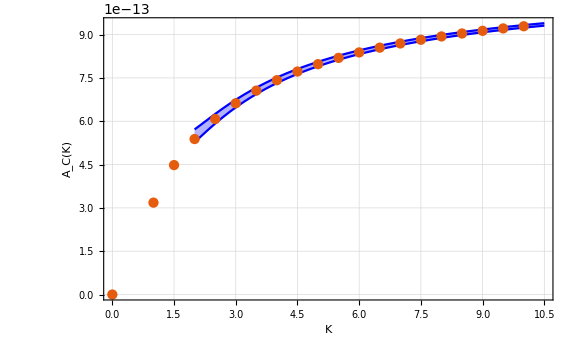

```mathematica
Show[Plot[{fit1,fit2},{k,2,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolationg1,PlotRange->All],PlotRange->All]
```